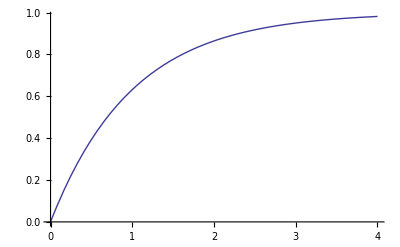

```mathematica
Plot[Evaluate[Integrate[Exp[-x],{x,0,t}]],{t,0,4},PlotRange->All]
```

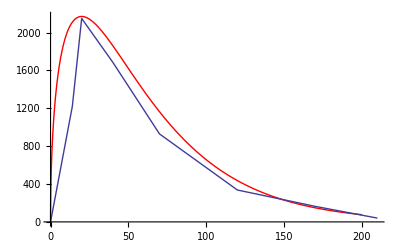

```mathematica
Show[
Plot[800 √(x)Exp[(-(x))/40],{x,0,200},PlotStyle->Red,PlotRange->All],
ListPlot[data1,Joined-> True]

]
```

```mathematica
data1
```

{{0,0},{14,1220},{20,2149},{40,1686},{70,929},{120,337},{170,164},{210,40}}

{a→17.3353,b→98.3016,c→27.5106}

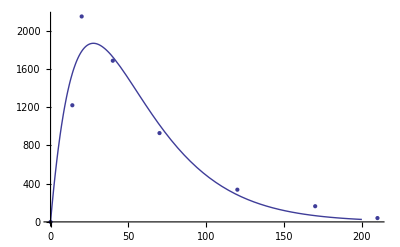

```mathematica
data1={
{0,0},
{14,1220},
{20,2149},
{40,1686},
{70,929},
{120, 337},
{170,164},
{210,40}};
fitting1=FindFit[data1,b x Exp[(-(x-a))/c],{a,b,c},x]
Show[
ListPlot[data1],
Plot[Evaluate[b x Exp[(-(x-a))/c]/.fitting1],{x,00,200}]
]
```

```mathematica
Integrate[Evaluate[b x Exp[(-(x-a))/c]/.fitting1],{x,0,t}]
```

184.597 (756.833+ⅇ^(-0.0363496 t) (-756.833-27.5106 t))

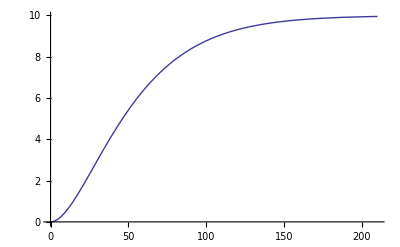

```mathematica
Plot[184.59679065691415 (756.8333003558201+ⅇ^(-0.03634962072077783 t) (-756.8333003558201-27.51060341678859 t))/14000,{t,0,210}]
```

```mathematica
184.59679065691415 (756.8333003558201+ⅇ^(-0.03634962072077783 t) (-756.8333003558201-27.51060341678859 t))/14000/.{t->1900-1680}
```

9.949

-5832.25+9.08611 x-0.00470397 x^2+8.10587×10^-7 x^3

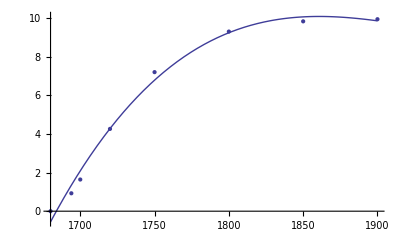

```mathematica
data1={
{1680,0},
{1694,0.927},
{1700,1.64},
{1720,4.26},
{1750,7.2},
{1800, 9.3},
{1850,9.83},
{1900,9.94}};
fitting1=Fit[data1,{1,x,x^2,x^3},x]
Show[
Plot[fitting1,{x,1680,1900}],
ListPlot[data1]
]
```

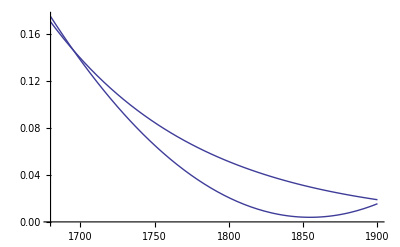

```mathematica
Show[
Plot[Evaluate[D[fitting1,x]],{x,1680,1900}],
Plot[0.17Exp[(-(x-1680))/100],{x,1680,1900}]
]
```

6.69306+0.0482158 x-0.0000930821 x^2-5.30404×10^-7 x^3

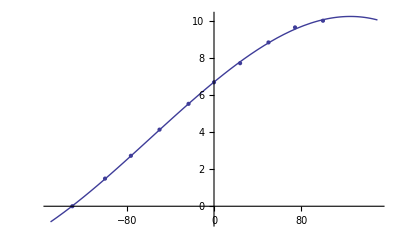

```mathematica
data2={
{-130,0},
{-100,1.49},
{-76.27,2.72},
{-50.00,4.13},
{-23.36,5.52},
{0.0000, 6.68},
{23.94,7.71},
{50.00,8.83},
{74.36,9.64},
{100,10}};
fitting2=Fit[data2,{1,x,x^2,x^3},x]
Show[
Plot[fitting2,{x,-150,150}],
ListPlot[data2]
]
```

6.32036+0.0482623 x-0.0000634076 x^2-4.8644×10^-7 x^3

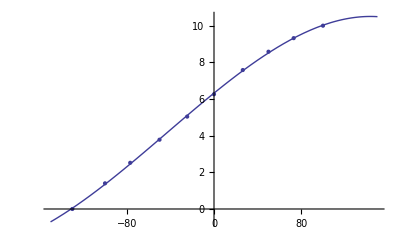

```mathematica
data3={
{-130,0},
{-100,1.40},
{-76.89,2.52},
{-50.00,3.78},
{-24.61,5.04},
{0.0000, 6.26},
{26.43,7.58},
{50.00, 8.58},
{73.12,9.32},
{100,10}};
fitting3=Fit[data3,{1,x,x^2,x^3},x]
Show[
Plot[fitting3,{x,-150,150}],
ListPlot[data3]
]
```

6.76723+0.0469663 x-0.0000995028 x^2-4.67342×10^-7 x^3

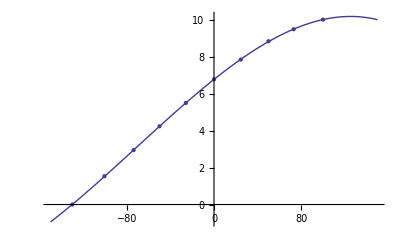

```mathematica
data4={
{-130,0},
{-100.55,1.53},
{-73.78,2.94},
{-50,4.23},
{-25.85,5.49},
{0, 6.77},
{24.57,7.84},
{50, 8.83},
{73.12,9.48},
{100,10}};
fitting4=Fit[data4,{1,x,x^2,x^3},x]
Show[
Plot[fitting4,{x,-150,150}],
ListPlot[data4]
]
```

6.70199+0.0467231 x-0.0000916216 x^2-4.21856×10^-7 x^3

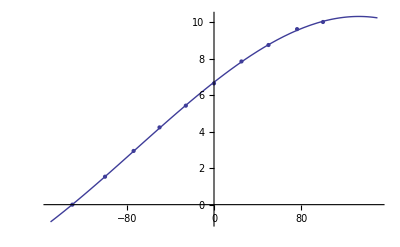

```mathematica
data5={
{-130,0},
{-100,1.53},
{-73.78,2.94},
{-50,4.23},
{-25.85,5.42},
{0,6.64},
{25.19,7.84},
{50,8.74},
{76.23,9.61},
{100,10}};
fitting5=Fit[data5,{1,x,x^2,x^3},x]
Show[
Plot[fitting5,{x,-150,150}],
ListPlot[data5]
]
```

6.55591+0.0482003 x-0.0000844948 x^2-5.21826×10^-7 x^3

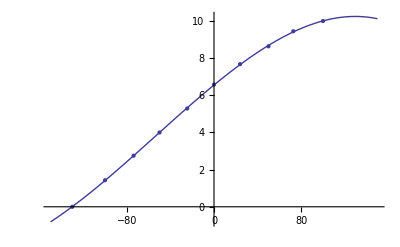

```mathematica
data6={
{-130,0},
{-100,1.43},
{-73.78,2.75},
{-50, 4},
{-24.61,5.29},
{0, 6.58},
{23.94,7.68},
{50, 8.64},
{72.76,9.45},
{100,10}};
fitting6=Fit[data6,{1,x,x^2,x^3},x]
Show[
Plot[fitting6,{x,-150,150}],
ListPlot[data6]
]
```

```mathematica
fittingorg2[x_]:= 7.67+0.0464x-16.89 10^-5 x^2-6.313 10^-7 x^3
```

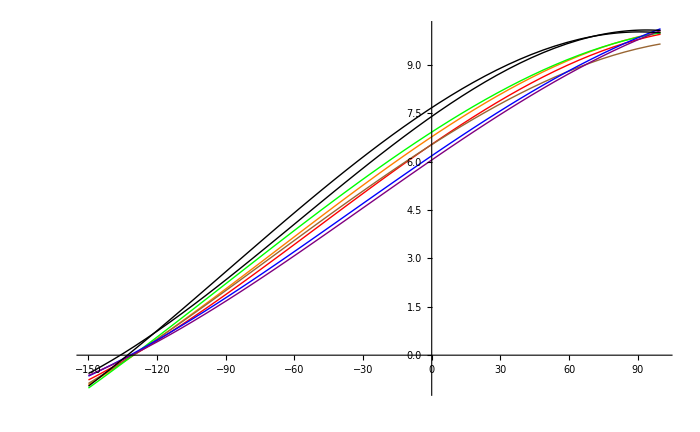

```mathematica
Plot[{fitting1,fitting2,fitting3,fitting4,fitting5,fitting6,fittingOrg},{x,-150,100},PlotStyle->{Red,Orange,Brown,Green, Blue,Purple,Black,Black},ImageSize->700]
```

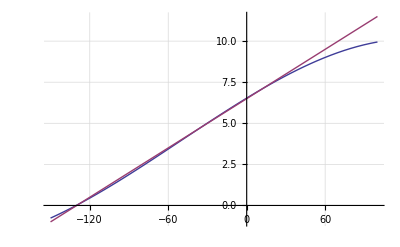

```mathematica
Plot[{fitting1,(x+130)/20},{x,-150,100},GridLines->Automatic]
```

7.39832+0.0497652 x-0.000147677 x^2-8.35815×10^-7 x^3

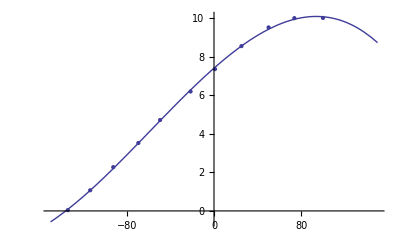

```mathematica
dataOrg={
{-134.16,0.04},
{-113.62,1.07},
{-92.46,2.27},
{-69.43,3.52},
{-49.51,4.71},
{-21.50,6.19},
{0.91,7.35},
{25.19,8.54},
{50.09,9.51},
{73.74,9.99},
{100,10}};
fittingOrg=Fit[dataOrg,{1,x,x^2,x^3},x]
Show[
Plot[fittingOrg,{x,-150,150}],
ListPlot[dataOrg]
]
```